```mathematica
(*
x' = x(2-0.01y)
y' = -y(1-0.01x)
A) Solve numerically using NDSolve
B)Plot numerical Solutions
C) Parametric Plot of solutions
D) Ananlyse the plots
*)

eq1 = x'[t] == x[t](2-0.01 y[t]);
```

```mathematica
eq2 = y'[t] == -y[t](1-0.01x[t]);


(*x[0] = 300, y[0] = 150*)
```

```mathematica
sol1 = NDSolve[{eq1,eq2, x[0] == 300, y[0] == 150},{x[t], y[t]},{t,0,10} ]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

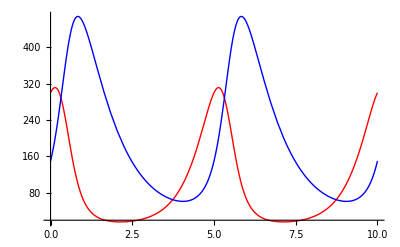

```mathematica
plot1 = Show[
Plot[Evaluate[x[t]/.sol1], {t,0,10}, PlotRange->All, PlotStyle->{Red}],
Plot[Evaluate[y[t]/.sol1], {t,0,10}, PlotRange->All, PlotStyle->{Blue}]
]
```

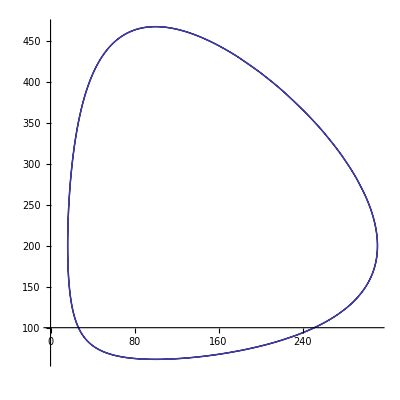

```mathematica
pplot1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol1], {t,0,10},AspectRatio->1]
```

```mathematica
(*x[0] = 150, y[0] = 200*)
sol2 = NDSolve[{eq1,eq2, x[0] == 150, y[0] == 200},{x[t], y[t]},{t,0,10} ]
```

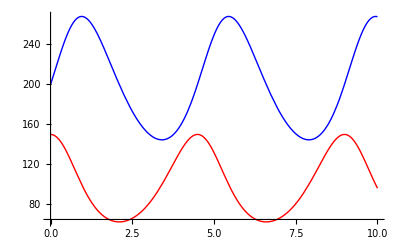

```mathematica
plot2 = Show[
Plot[Evaluate[x[t]/.sol2], {t,0,10}, PlotRange->All, PlotStyle->{Red}],
Plot[Evaluate[y[t]/.sol2], {t,0,10}, PlotRange->All, PlotStyle->{Blue}]
]
```

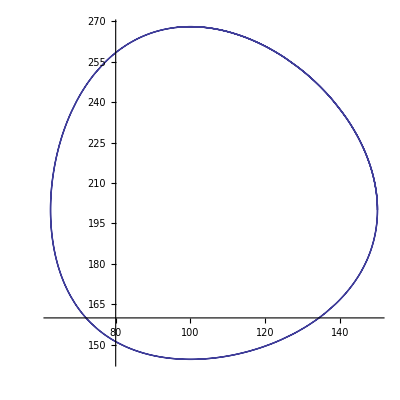

```mathematica
pplot2 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol2], {t,0,10},AspectRatio->1]
```

```mathematica
(*x[0]=120, y[0] = 200*)
sol3 = NDSolve[{eq1, eq2, x[0] == 120, y[0]== 200},{x[t], y[t]}, {t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

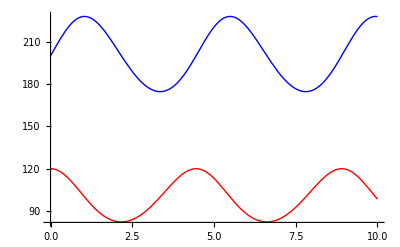

```mathematica
plot3 = Show[
Plot[Evaluate[x[t]/.sol3], {t,0,10}, PlotRange->All, PlotStyle->{Red}],
Plot[Evaluate[y[t]/.sol3], {t,0,10}, PlotRange->All, PlotStyle->{Blue}]
]
```

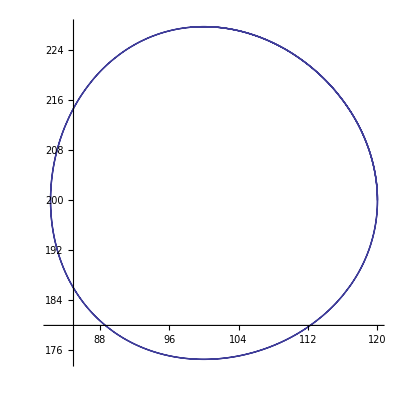

```mathematica
pplot3 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol3], {t,0,10},AspectRatio->1]
```

```mathematica
(*x[0] = 100, y[0] = 200*)
sol4 = NDSolve[{eq1, eq2, x[0] == 100, y[0]== 200},{x[t], y[t]}, {t,0,10}]
plot4 = Show[
Plot[Evaluate[x[t]/.sol4], {t,0,10}, PlotRange->All, PlotStyle->{Red}],
Plot[Evaluate[y[t]/.sol4], {t,0,10}, PlotRange->All, PlotStyle->{Blue}]
]
pplot4 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol4], {t,0,10},AspectRatio->1]
```

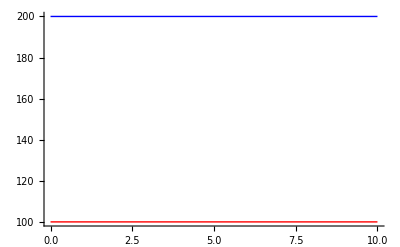

ListPlot::nonopt: Options expected (instead of 010) beyond position 1 in {{TagBox[InterpolatingFunction[{{0.`, 10.`}}, {4, 23, 1, {13}, {4}, 0, 0, 0, 0, Automatic}, {{0.`, 0.0010264848819015065`, 0.002052969763803013`, 1.002052969763803`, 2.002052969763803`, 3.002052969763803`, 4.0020529697638025`, 5.0020529697638025`, 6.0020529697638025`, 7.0020529697638025`, 8.002052969763803`, 9.001026484881901`, 10.`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12, 14, 16, 18, 20, 22, 24, 26}, {100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`, 100.`, 0.`}}, {Automatic}], False, Rule[Editable, False]][GraphicsBox[List[List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]]], List[Rule[PlotRange, All], Rule[AspectRatio, 1], Rule[Axes, True], Rule[AxesOrigin, List[Skeleton[2]]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]], TagBox[InterpolatingFunction[{{0.`, 10.`}}, {4, 23, 1, {13}, {4}, 0, 0, 0, 0, Automatic}, {{0.`, « 11 », 10.`}}, {« 1 »}, {Automatic}], False, Rule[Editable, False]][GraphicsBox[List[List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]], List[List[Skeleton[3]]]], List[Rule[PlotRange, All], Rule[AspectRatio, 1], Rule[Axes, True], Rule[AxesOrigin, List[Skeleton[2]]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]]}}, {GraphicsBox[List[List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[AspectRatio, 1], Rule[Axes, True], Rule[AxesOrigin, List[0, 100.`]], Rule[PlotRange, List[List[0.`, 311.2022187910517`], List[61.35850394099629`, 467.48471084331226`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], 0, 10}. An option must be a rule or a list of rules.

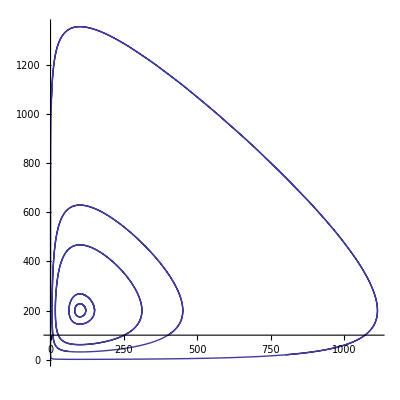
ListPlot[{{InterpolatingFunction[{{0.,10.}},<>][-Graphics-],InterpolatingFunction[{{0.,10.}},<>][-Graphics-]}},{-Graphics-,0,10}]

```mathematica
(*equilibrium case*)

lplot4 = ListPlot[{x[t],y[t]}/.sol4, {t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

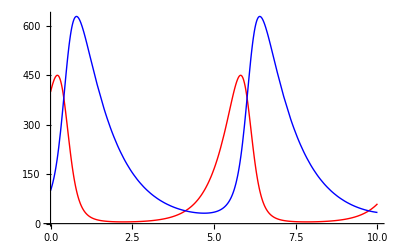

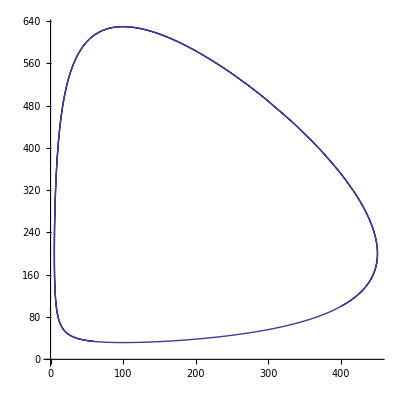

```mathematica
(*x[0] = 400, y[0] = 100*)
sol5 = NDSolve[{eq1, eq2, x[0] == 400, y[0]== 100},{x[t], y[t]}, {t,0,10}]
plot5 = Show[
Plot[Evaluate[x[t]/.sol5], {t,0,10}, PlotRange->All, PlotStyle->{Red}],
Plot[Evaluate[y[t]/.sol5], {t,0,10}, PlotRange->All, PlotStyle->{Blue}]
]
pplot5 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol5], {t,0,10},AspectRatio->1]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

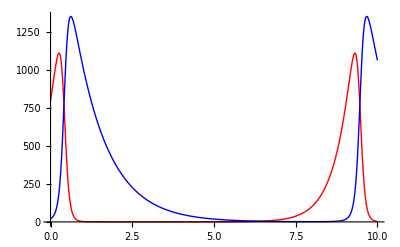

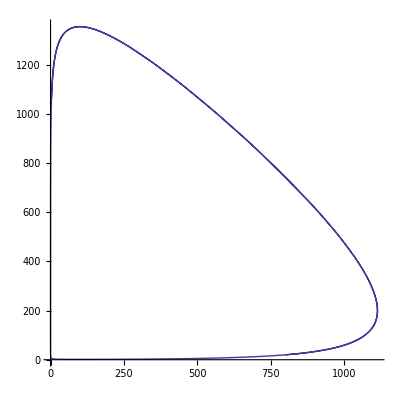

```mathematica
(*x[0] = 800, y[0] = 20*)
sol6 = NDSolve[{eq1, eq2, x[0] == 800, y[0]== 20},{x[t], y[t]}, {t,0,10}]
plot6 = Show[
Plot[Evaluate[x[t]/.sol6], {t,0,10}, PlotRange->All, PlotStyle->{Red}],
Plot[Evaluate[y[t]/.sol6], {t,0,10}, PlotRange->All, PlotStyle->{Blue}]
]
pplot6 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol6], {t,0,10},AspectRatio->1,PlotRange->All]
```

```mathematica
(*Show all together*)
t = Show[pplot1,pplot2,pplot3,pplot4,pplot5,pplot6, PlotRange->All]
```

-Graphics-